## Задание 1.1

```mathematica
exp = (4(x^3+ 9)(x^2-y^2))/((9 x^2-16)(x-y))+2(x+y)^2+x^3+y^3
```

x^3+y^3+2 (x+y)^2+(4 (9+x^3) (x^2-y^2))/((-16+9 x^2) (x-y))

```mathematica
Expand[exp](* Раскрывает скобки, производя умножения и возведения в степень и представляя результат в виде суммы *)
```

2 x^2+x^3+(36 x^2)/((-16+9 x^2) (x-y))+(4 x^5)/((-16+9 x^2) (x-y))+4 x y+2 y^2-(36 y^2)/((-16+9 x^2) (x-y))-(4 x^3 y^2)/((-16+9 x^2) (x-y))+y^3

```mathematica
ExpandAll[exp](* Применяет функцию Expand как к числителю, так и знаменателю *)
```

2 x^2+x^3+4 x y+2 y^2+y^3+(36 x^2)/(-16 x+9 x^3+16 y-9 x^2 y)+(4 x^5)/(-16 x+9 x^3+16 y-9 x^2 y)-(36 y^2)/(-16 x+9 x^3+16 y-9 x^2 y)-(4 x^3 y^2)/(-16 x+9 x^3+16 y-9 x^2 y)

```mathematica
Factor[exp](* Представляет выражение в виде произведения множителей *)
```

((x+y) (36-32 x-16 x^2+22 x^3+9 x^4-32 y+16 x y+18 x^2 y-9 x^3 y-16 y^2+9 x^2 y^2))/((-4+3 x) (4+3 x))

```mathematica
Together[exp](* Приводит к общему знаменателю *)
```

(36 x-32 x^2-16 x^3+22 x^4+9 x^5+36 y-64 x y+40 x^3 y-32 y^2+18 x^2 y^2-16 y^3+9 x^2 y^3)/(-16+9 x^2)

```mathematica
Apart[exp](* Переписывает рациональное выражение как сумму дробей с простыми знаменателями *)
```

(x (36-32 x-16 x^2+22 x^3+9 x^4))/((-4+3 x) (4+3 x))+(4 (9-16 x+10 x^3) y)/((-4+3 x) (4+3 x))+2 y^2+y^3

```mathematica
Cancel[exp](* Сокращает общие множители в числителе и знаменателе *)
```

x^3+y^3+(4 (9+x^3) (x+y))/(-16+9 x^2)+2 (x+y)^2

```mathematica
Simplify[exp](* Находит простейшую форму *)
```

x^3+y^3+(4 (9+x^3) (x+y))/(-16+9 x^2)+2 (x+y)^2

## Задание 1.2

```mathematica
num = Numerator[Together[exp]](* Возвращает числитель *)
```

36 x-32 x^2-16 x^3+22 x^4+9 x^5+36 y-64 x y+40 x^3 y-32 y^2+18 x^2 y^2-16 y^3+9 x^2 y^3

```mathematica
Collect[num, x](* Представляет выражаение в виде полинома по степеням x *)
```

22 x^4+9 x^5+x (36-64 y)+36 y-32 y^2-16 y^3+x^3 (-16+40 y)+x^2 (-32+18 y^2+9 y^3)

```mathematica
Collect[num,y]
```

36 x-32 x^2-16 x^3+22 x^4+9 x^5+(36-64 x+40 x^3) y+(-32+18 x^2) y^2+(-16+9 x^2) y^3

```mathematica
Exponent[num,x] (* Возвращает максимальную степень множителя *)
```

5

```mathematica
Exponent[num,y]
```

3

```mathematica
Coefficient[num,x,5](* Возвращает коэффициет при множителе *)
```

9

```mathematica
Coefficient[num, y, 3]
```

-16+9 x^2

## Задание 2.1

```mathematica
D[x^n Cos[x],x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

## Задание 2.2

```mathematica
D[a x^3+2 x^2,x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5 x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[ x^3 y^2+3 x^2,{x,3},{y,2}]
```

12

## Задание 2.3

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

## Задание 2.4

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[x^2/2-1/2 Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
ExpandAll[Together[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]]
```

1/(1+x^3)

## Задание 2.5

```mathematica
Integrate[5x-2 √x+32/x^3,{x,1,4}]
```

259/6

## Задание 2.6

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1}]
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}]
```

1.05753

## Задание 3.1

```mathematica
Solve[a x^4+x^2+3==0,x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

## Задание 3.2

```mathematica
Solve[x^2+y==1&&y^2-x^2==2,{x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

## Задание 3.3

```mathematica
NSolve[x^2-y^2==1 && y^3+x==5,{x,y}](* Приближения к решениям *)
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

## Задание 3.4

```mathematica
DSolve[y'[x]-y[x]Tan[x]==x,y[x],x]
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
DSolve[{y'[x]-y[x]Tan[x]==x,y[0]==0},y[x],x]
```

{{y[x]→1-Sec[x]+x Tan[x]}}

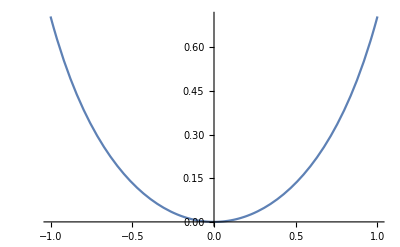

```mathematica
Plot[1-Sec[x]+x Tan[x],{x,-1,1}]
```

```mathematica
DSolve[y'[x]+y[x]Tan[x]==1/Cos[x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

```mathematica
DSolve[{y'[x]+y[x]Tan[x]==1/Cos[x],y[0]==0},y[x],x]
```

{{y[x]→Sin[x]}}

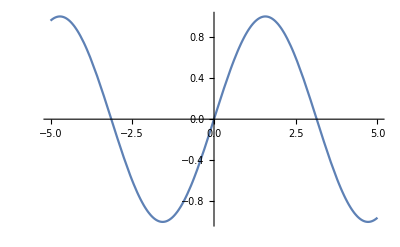

```mathematica
Plot[Sin[x],{x,-5,5}]
```

## Задание 3.5

```mathematica
DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==0, y'[0]==1}, y[x], x]
```

{{y[x]→-((-1)^(2/3) ⅇ^(x/2) (AiryAi[-(-1)^(1/3) (1/4-x)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]))/(AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)])}}

```mathematica
NDSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==0, y'[0]==1}, y[x], {x, -5,5}]
```

{{y[x]→InterpolatingFunction[…][x]}}

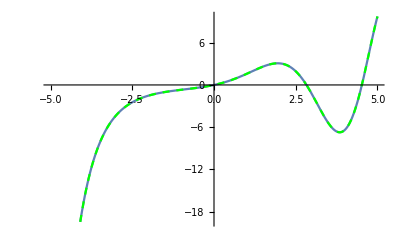

```mathematica
Show[Plot[InterpolatingFunction[…][x],{x,-5,5}],Plot[-((-1)^(2/3) ⅇ^(x/2) (AiryAi[-(-1)^(1/3) (1/4-x)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]))/(AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)]),{x,-5,5},PlotStyle->{Dashed, Green}]]
```